# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"package/"];
Get["funcs_rxns_moms.m"]
```

# Import

## Import function

```mathematica
getDir[noIP3R_,ip3_,dataDesc_]:=Module[
{}
,
If[noIP3R<1000,
Return[NotebookDirectory[]<>"../stochastic_simulations/ml_training_data/data_gillespie/vol_exp_"<>ToString[dataDesc["volExp"]]<>"/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/"],
Return[NotebookDirectory[]<>"../stochastic_simulations/ml_training_data/data_tau_leaping/vol_exp_"<>ToString[dataDesc["volExp"]]<>"/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/"]
];
Return[NotebookDirectory[]];
]
```

```mathematica
importAndWhitenAndCalcParams[nv_,nh_,ip3_,noIP3R_,dataDesc_,muhs_,varhs_,mv_,sv_]:=Module[
{data,d1,d2,dims,mvArr,svArr,dataS,params,paramsLD,tpt,nd}
,
SetDirectory[getDir[noIP3R,ip3,dataDesc]];
data=importData[dataDesc,noIP3R]//N;
data=data[[(dataDesc["tptStart"]);;(dataDesc["tptMax"]);;dataDesc["tptInterval"]]];

dims=Dimensions[data][[;;2]];
mvArr=ConstantArray[mv,dims];
svArr=ConstantArray[sv,dims];

dataS=(data-mvArr)/svArr;

paramsLD={};
Do[
AppendTo[paramsLD,getMLparams[dataS[[i]],muhs[[i]],varhs[[i]]]];
,{i,dataDesc["noTpts"]}];

params=makePStructFromLD[nv,nh,paramsLD];

Return[params]
]
```

## Data description

```mathematica
noSeeds=100;
tptStart=100;
tptMax=500;
tptInterval=1;
dt=0.1;
volExp=14;

dataDesc=makeDataDesc[noSeeds,volExp,tptStart,tptMax,tptInterval,dt];
noTpts=dataDesc["noTpts"];
times=dataDesc["times"];
```

```mathematica
cdir=getCacheDir[dataDesc];
exportDataDesc[dataDesc,cdir<>"data_desc.txt"]
```

## Setup latent space

```mathematica
nv=3;
nh=1;
```

```mathematica
muhs={};
varhs={};
Do[
AppendTo[muhs,ConstantArray[0,nh]//N];
AppendTo[varhs,IdentityMatrix[nh]//N];
,{tpt,tptStart,tptMax,tptInterval}];
```

## Calculate and export transformation

```mathematica
importVizTrans[ip3_,noIP3R_,dataDesc_,noSeeds_:-1]:=Module[
{data0,dataDesc0}
,
SetDirectory[getDir[noIP3R,ip3,dataDesc]];

dataDesc0=dataDesc;
If[noSeeds>0,
dataDesc0["noSeeds"]=noSeeds;
];
data0=importData[dataDesc0,noIP3R];
data0=data0[[(tptStart+1);;(tptMax+1);;tptInterval]];

Return[data0]
]
```

```mathematica
dataVizTrans=Association[];
Do[
Do[
dataVizTrans[{noIP3R,ip3}]=importVizTrans[ip3,noIP3R,dataDesc,1];
,{noIP3R,{100,1000,5000}}];
,{ip3,{"ip3_0p100","ip3_2p000"}}];
```

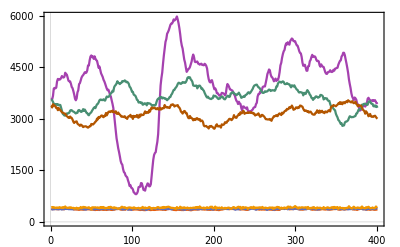

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
Row[{
ListLinePlot[Values[dataVizTrans][[;;,;;,1,1]]],
LineLegend[colors[[;;Length[Keys[dataVizTrans]]]],Keys[dataVizTrans]]
}]
```

```mathematica
data0=importVizTrans["ip3_0p100",100,dataDesc];
data1=importVizTrans["ip3_2p000",5000,dataDesc];
```

```mathematica
m0=Mean[Mean[data0]]//N
m1=Mean[Mean[data1]]//N
mv=Mean[{m0,m1}]
```

{363.913,597.564,100.}

{3135.65,12311.4,5000.}

{1749.78,6454.46,2550.}

```mathematica
dataTog=Flatten[Join[data0,data1]];
sv=Sqrt[Sum[(x-mv)^2,{x,dataTog}]/Length[dataTog]]
```

{1392.37,5856.93,2450.}

```mathematica
(*
SetDirectory[NotebookDirectory[]];
s=StringRiffle[ToString@PaddedForm[#,16]&/@mv," "];
s=s<>"\n";
s=s<>StringRiffle[ToString@PaddedForm[#,16]&/@sv," "];

cdir=getCacheDir[dataDesc];
Export[cdir<>"transformations.txt",s];
*)
```

## Import transformation

```mathematica
cdir=getCacheDir[dataDesc];
{mv,sv}=Import[cdir<>"transformations.txt","Table"]
```

{{1749.78,6454.46,2550.},{1392.37,5856.93,2450.}}

## Import for cache and export to cache

```mathematica
exportToCache[nv_,nh_,params_,dataDesc_,ip3_,noIP3R_]:=Module[
{cdir,x}
,
cdir=getCacheDir[dataDesc,noIP3R]<>"params0/";

If[!DirectoryQ[cdir<>ip3],CreateDirectory[cdir<>ip3]];
Do[
x=params["LFDL"][k];
Export[cdir<>ip3<>"/"<>k<>".txt",StringRiffle[ToString[#,FortranForm]&/@PaddedForm[#,16]&/@x,"\n"]]
,{k,makeLF[nv,nh]}];
]
```

```mathematica
noIP3Rs={100,500,600,700,800,900,1000,1500,2000,2500,3000,3500,4000,4500,5000};
(*
noIP3Rs={900};
*)

ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};
(*
ip3s={"ip3_0p100"};
*)

Monitor[
Do[
noIP3R=noIP3Rs[[idx2]];

Monitor[
Do[
ip3=ip3s[[idx]];
params=importAndWhitenAndCalcParams[nv,nh,ip3,noIP3R,dataDesc,muhs,varhs,mv,sv];
exportToCache[nv,nh,params,dataDesc,ip3,noIP3R];
,{idx,Length[ip3s]}];
,Row[{"IP3: ",ProgressIndicator[idx,{1,Length[ip3s]}]}]]

,{idx2,Length[noIP3Rs]}];
,Row[{"# IP3Rs: ",ProgressIndicator[idx2,{1,Length[noIP3Rs]}]}]]
```

# Re import and viz

## Import cache

```mathematica
nv=3;
nh=1;

volExp=14;
cdir=getCacheDirRaw[volExp];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];

ip3Keys={};
Do[
AppendTo[ip3Keys,{noIP3R,ip3}];
,{ip3,ip3s}
,{noIP3R,noIP3Rs}];

params0=Association[];
Do[
{noIP3R,ip3}=ip3Key;

cdir=getCacheDirRaw[volExp,noIP3R];
pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"params0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

params0[ip3Key]=makePStructFromLFDL[nv,nh,pLFDL];
,{ip3Key,ip3Keys}];
```

## Viz

```mathematica
ip3sPlt={
"ip3_0p100","ip3_0p400","ip3_0p700","ip3_1p000",
"ip3_1p300","ip3_1p600","ip3_1p900"
}

pltEvery=20;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3sPlt]],{i,Length[ip3sPlt]}]
```

{ip3_0p100,ip3_0p400,ip3_0p700,ip3_1p000,ip3_1p300,ip3_1p600,ip3_1p900}

{RGBColor[0.584692, 0.44694657142857147, 0.3233],RGBColor[0.756208, 0.6565245714285715, 0.5653625714285714],RGBColor[0.8283884285714286, 0.8146152857142858, 0.7674522857142857],RGBColor[0.7939004285714286, 0.9150341428571429, 0.9120654285714286],RGBColor[0.6742975714285715, 0.9295297142857143, 0.965857],RGBColor[0.5239352857142857, 0.863684, 0.9428224285714286],RGBColor[0.342992, 0.650614, 0.772702]}

```mathematica
lfPlt=Select[makeLF[nv,nh],StringLength[#]<4||(StringTake[#,4]!="varh"&&StringTake[#,3]!="muh")&]
```

{wt11,wt12,wt13,sig2,b1,b2,b3}

```mathematica
rngs=<|
"wt11"->{0,1.4},
"wt12"->{-0.01,0.01},
"wt13"->{-0.00001,0.00001},
"sig2"->{0,10^-4},
"b1"->{-1.0,2.0},
"b2"->{-1.3,1.3},
"b3"->{-2,2}
|>;

plts=Table[
Table[
Show[
Table[
ip3=ip3sPlt[[i]];
ip3Key={noIP3R,ip3};
xPlt=params0[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->labels[k],PlotStyle->colors[[i]]]
,{i,Length[ip3sPlt]}],
PlotRange->rngs[k],
PlotLabel->ToString[noIP3R]<>" "<>labels[k],
FrameLabel->{"Time (s)"}
]
,{noIP3R,{100,1000,3000,5000}}]
,{k,lfPlt}];
```

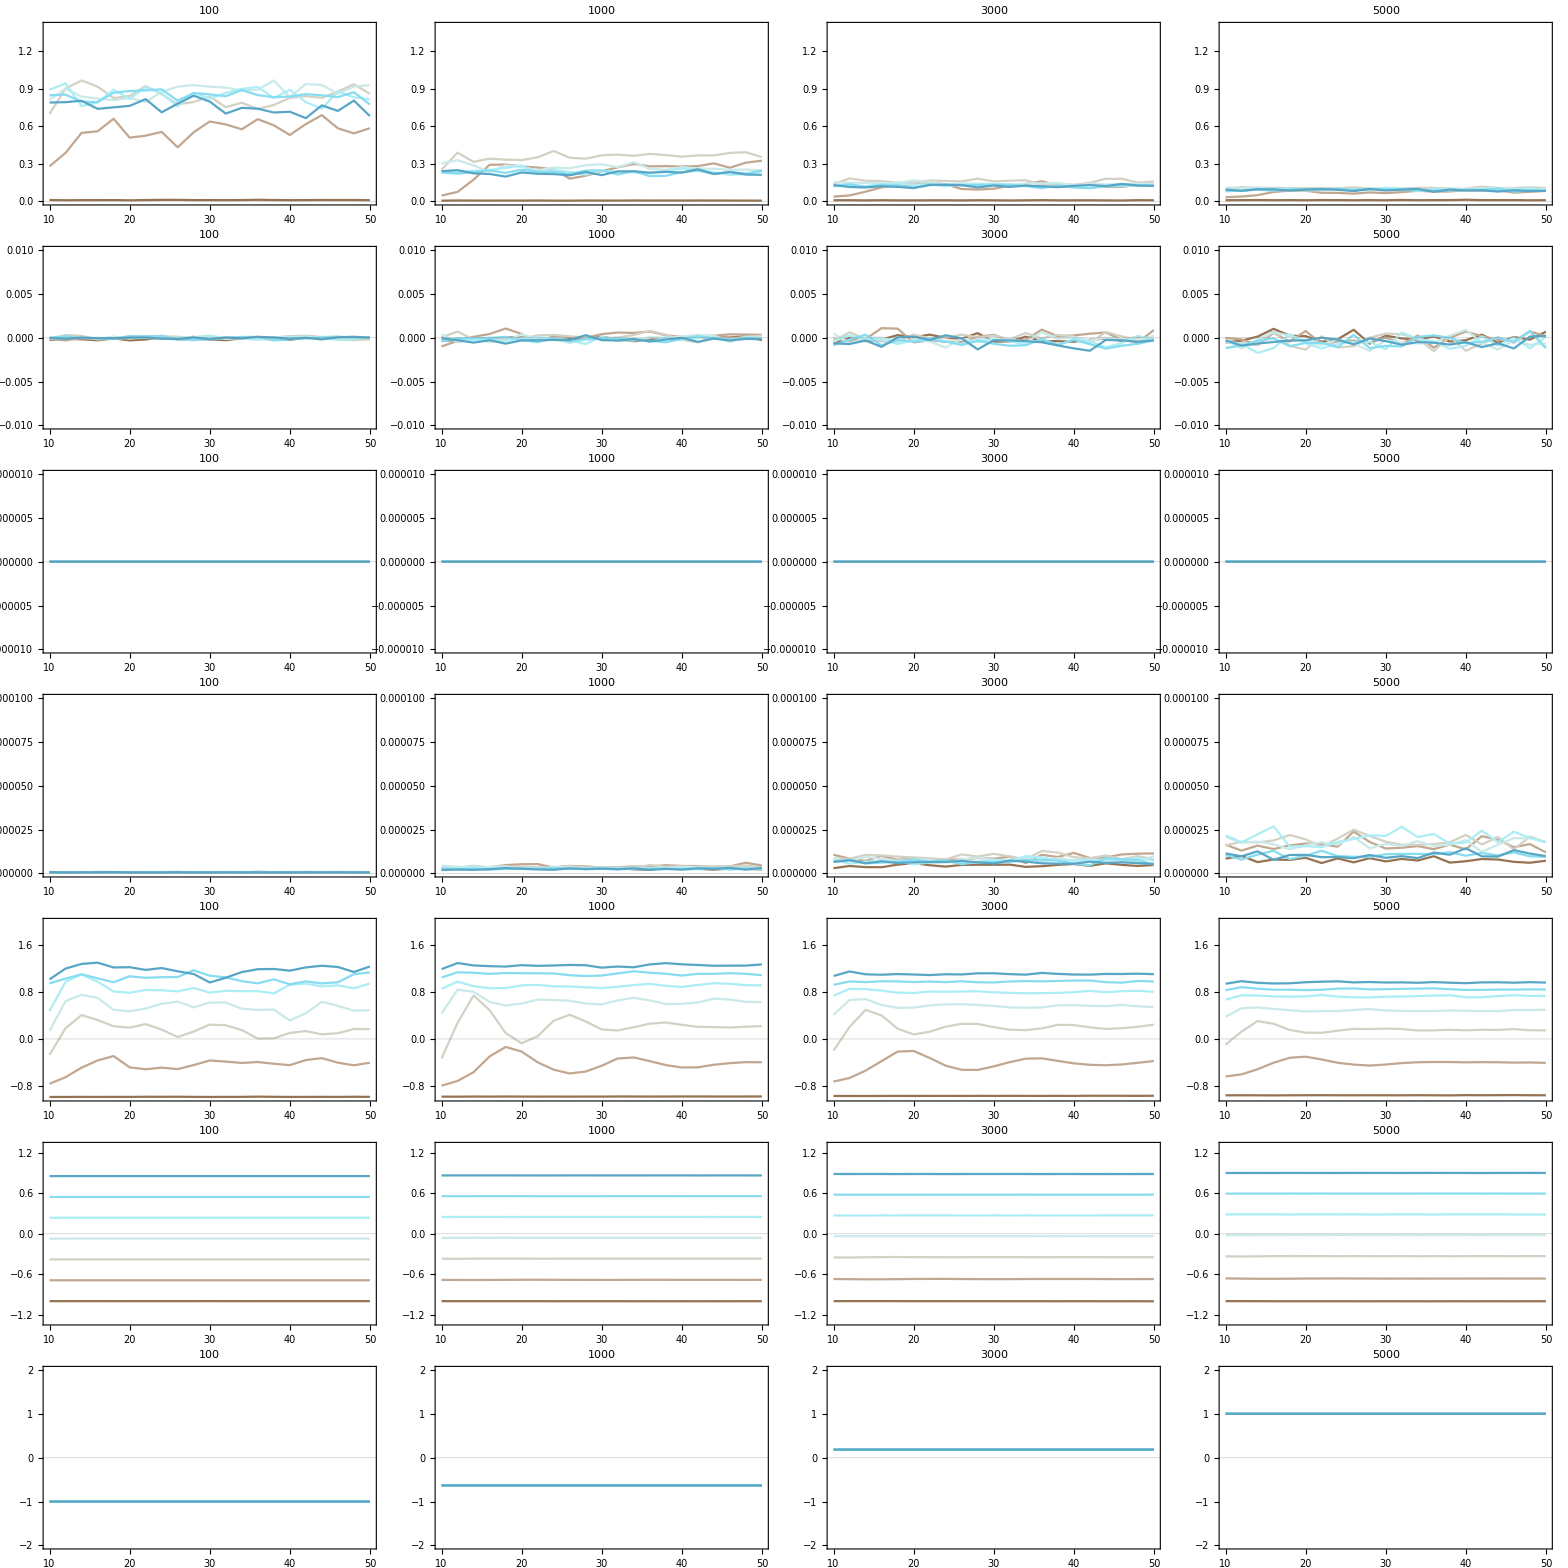

```mathematica
Grid[plts]
```